```mathematica
<< VarCleanup`;
<< PenduloComPolia`Importador`;
<< PenduloComPolia`ModeloEDO`;
<< PenduloComPolia`ModeloGeometrico`;
```

```mathematica
VarCleanup`RemoveGlobal[];
```

Remove::rmnsm: There are no symbols matching "Global`*".

## Modelo matemático por EDOs

```mathematica
θ[tempo_]=Module[{t},
ReplaceAll[SolucaoNumerica[0,8,t],{t->tempo}]
];
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

### Gráfico

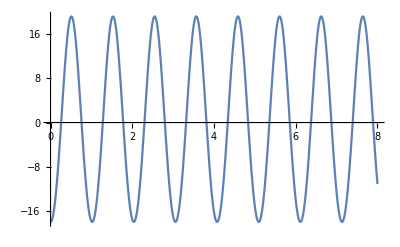

```mathematica
Plot[θ[t]/Degree, {t,0,8}]
```

## Tomadas

```mathematica
x = Listar[2,"t", "x", "y"];
```

Comparar com uma teórica

```mathematica
Clear[posicoesX]
```

```mathematica
tempos = Listar[3, "t"];
posicoesX[tempo_] = X[Pegar["raio da polia"],Pegar["comprimento do fio"],theta[t]]/.theta[t]->θ[tempo];
```

```mathematica
tabelaX = Table[{Part[tempos,i],posicoesX[Part[tempos,i]]}//Flatten,{i,1,800}];
```

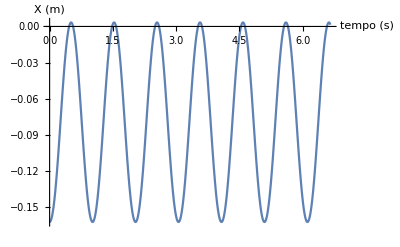

```mathematica
ListLinePlot[tabelaX, AxesLabel->{"tempo (s)","X (m)"}]
```

### Teste

```mathematica
Show[
ListPointPlot3D[x],
AxesLabel->{"tempo","posição X","posição Y"},
PlotRange->All,
ImageSize->Full
]
```